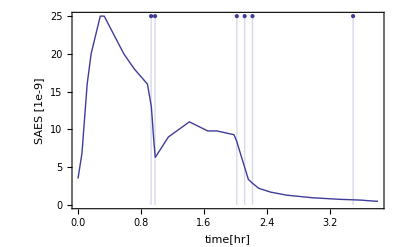

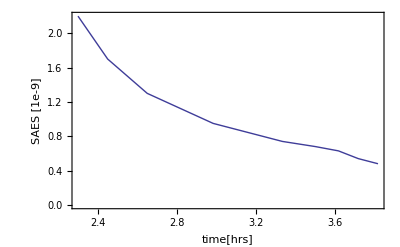

```mathematica
times={3,57,4,00,4,04,4,07,4,14,4,17,4,23,4,32,4,40,4,50,4,53,4,55,4,56,5,06,5,22,5,36,5,43,5,56,5,58,6,07,6,10,6,15,6,24,6,36,6,56,7,06,7,17,7,27,7,34,7,40,7,46};
times=Partition[times,2];
times={1,1/60}.#&/@times;
times=times-times[[1]];
pressure={3.5,6.8,16,20,25,25,23,20,18,16,13,8.2,6.3,9,11,9.8,9.8,9.3,8.5,3.4,2.9,2.2,1.7,1.3,.95,.85,.74,.68,.63,.54,.48};
data=Thread[{times,pressure}];

markers={0.93,0.98,2.02,2.12,2.22,3.5};
markers={#,Max[pressure]}&/@markers;

Show[{ListPlot[data,Joined->True,Axes->False,Frame->True,FrameLabel->{"time[hr]","SAES [1e-9]"}],
ListPlot[markers,Filling->Axis]
}]
ListPlot[Cases[data,x_/;x[[1]]>2.22],Joined->True,PlotRange->{All,{0,2.2}},Axes->False,Frame->True,FrameLabel->{"time[hrs]","SAES [1e-9]"}]
```

## 0, Cs (3.00A), Na (3.80A) on. 0.93, Cs off. 0.98, Cs back on 2.02, Cs ->2.00A 2.12, Cs->1.00A 2.22, Cs-> off ~3.5, Na off

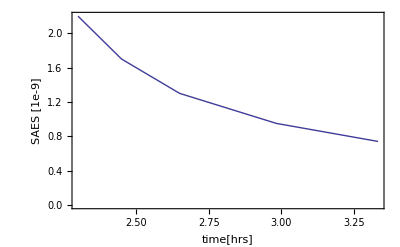

```mathematica
1. 7+30/60-(4)
```

3.5